```mathematica
nplus=K/(2(1+rho (S-1)))(1+Sqrt[1+(4 mu (1+rho (S-1)))/(r K)]);
lambda1=K-2 nplus(1+rho (S-1));
lambdan=K-nplus(2+rho (S-2));
ratioL=FullSimplify[lambdan/lambda1];
params={K-> 50.,r-> 1.,S-> 30.,rminus-> 1.};
```

```mathematica
firstDR=Simplify[D[ratioL,{mu,1}]/.params];
secondDR=Simplify[D[ratioL,{mu,2}]/.params];
secondDRrho=secondDR/.{rho-> 0.1};
Solve[secondDRrho==0,mu]
```

{{mu→3.26711×10^31}}

```mathematica
death1[rho_,mu_]:=(rminus+r/K(1+rho(S-1)K/(2(1+rho (S-1)))(1+Sqrt[1+(4 mu (1+rho (S-1)))/(r K)])))/.params;
```

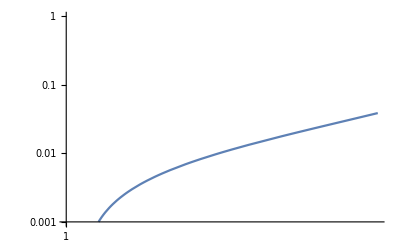

```mathematica
LogLogPlot[y/.Solve[death1[y,x]==x,y],{x,0.001,10.0},PlotRange->{10^-3,1}]
```

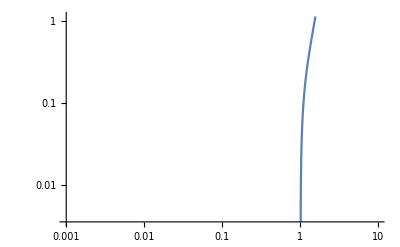

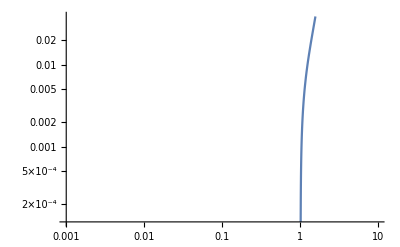

```mathematica
params1={K-> 50.,r-> 1.,S-> 2.,rminus-> 1.};
death1S[rho_,mu_]:=(rminus+r/K(1+K-1))/.params1;
LogLogPlot[y/.Solve[death1S[y,x]==x,y],{x,0.001,10.0}]
LogLogPlot[y/.Solve[death1[y,x]==x,y],{x,0.001,10.0}]
```